```mathematica
expapprox[x_,n_]:=(1+x/n)^-n
```

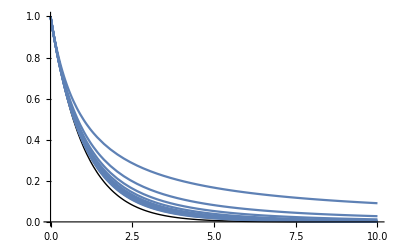

```mathematica
Show[
Plot[Exp[-x],{x,0,10}, PlotStyle->{Black,Thick}, PlotRange->{0,1}],
Plot[Table[expapprox[x,n],{n,1,10}],{x,0,10}, PlotRange->{0,1}]
]
```

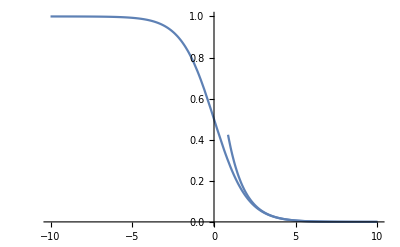

```mathematica
Show[
Plot[1/(1+Exp[x]),{x,-10,10}],
Plot[Exp[-x],{x,0,10}]
]
```

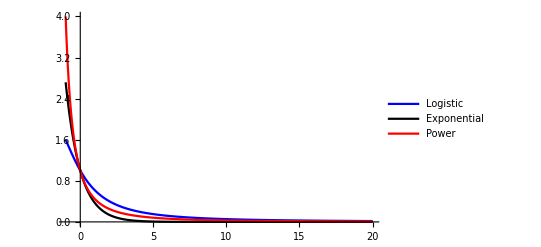

```mathematica
n = 2;
Show[
Plot[2/(1+(1 + x/n)^n),{x,-1,20}, PlotStyle->Blue, PlotRange->{0,All}, PlotLegends->{"Logistic"}],
Plot[Exp[-x],{x,-1,20}, PlotStyle->Black, PlotRange->{0,All}, PlotLegends->{"Exponential"}],
Plot[(1 + x/n)^-n,{x,-1,20}, PlotStyle->Red, PlotRange->{0,All},PlotLegends->{"Power"}]
]
```

```mathematica
g[d_, k_, ϕ_, α_, dstar_]:=(k (1 + (1 - (ϕ dstar)/α)^α))/(1 + (1 + (ϕ (d - dstar))/α)^α);
```

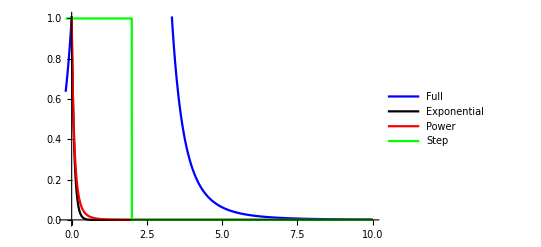

```mathematica
k = 1;
ϕ = 12;
α = 4;
dstar = 2;
Show[
Plot[g[d,k,ϕ,α,dstar],{d,-0.2,10}, PlotRange->{-0.01,k+0.01}, PlotStyle->Blue, PlotLegends->{"Full"}],
Plot[k Exp[-ϕ d],{d,-0.2,10}, PlotRange->{-0.01,k+0.01}, PlotStyle->Black, PlotLegends->{"Exponential"}],
Plot[k (1 + (ϕ d)/α)^-α,{d,-0.2,10}, PlotRange->{-0.01,k+0.01}, PlotStyle->Red, PlotLegends->{"Power"}],
Plot[Piecewise[{{k,d≤dstar},{0, d>dstar}}],{d,-0.2,10}, PlotRange->{-0.01,k+0.01}, PlotStyle->Green, PlotLegends->{"Step"}]
]
```